```mathematica
n=4;
razm=9;
TimesIter=10000;
incr=0;
pos0=(razm-1)/2+1;
posx=Table[Table[0,n+1],TimesIter];
posy=Table[Table[0,n+1],TimesIter];
```

```mathematica
For[j=0,j<TimesIter,j++,
PositionUD=pos0;
PositionRL=pos0;
posx[[j+1,1]]=PositionRL-pos0;
posy[[j+1,1]]=PositionUD-pos0;
res1=Table[Table[0,razm],razm];
res1[[pos0,pos0]]=1;
For[i=0,i<n,i++,
incr=RandomInteger[{1,4}];
If[incr==1,
res1[[PositionRL,PositionUD+1]]=res1[[PositionRL,PositionUD+1]]+1;
PositionUD=PositionUD+1;
];
If[incr==2,
res1[[PositionRL,PositionUD-1]]=res1[[PositionRL,PositionUD-1]]+1;
PositionUD=PositionUD-1;
];
If[incr==3,
res1[[PositionRL-1,PositionUD]]=res1[[PositionRL-1,PositionUD]]+1;
PositionRL=PositionRL-1;
];
If[incr==4,
res1[[PositionRL+1,PositionUD]]=res1[[PositionRL+1,PositionUD]]+1;
PositionRL=PositionRL+1;
];
posx[[j+1,i+2]]=PositionRL-pos0;
posy[[j+1,i+2]]=PositionUD-pos0;
]
]
```

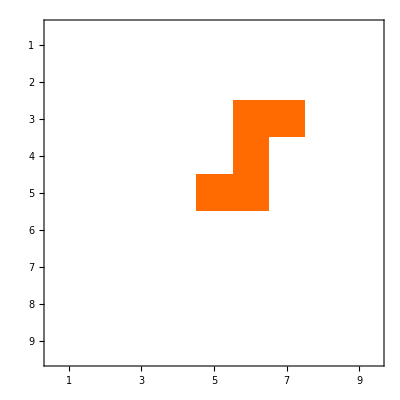

```mathematica
MatrixPlot[res1]
MatrixForm[posx];
xsr=0;
ysr=0;
Rsr=0;
For[j=1,j<=TimesIter,j++,
xsr=xsr+posx[[j,n]];
ysr=ysr+posy[[j,n]];
Rsr=posx[[j,n]]^2+posy[[j,n]]^2;
]
```

```mathematica
xsr=xsr/TimesIter
```

```mathematica
ysr=ysr/TimesIter
```

```mathematica
Rsr=Rsr/TimesIter
```

13/2500

-37/5000

1/2000